#### Phase boundary (non-normalized coordinates)

```mathematica
pdTxsmooth[x_]:=InterpolatingFunction[…][x]
pdRTxsmooth[x_]:=InterpolatingFunction[…][x]
singularitysmooth[x_]:=0.25 (-3.+x)^2 x;
Start[x_]:=ArcTan[InterpolatingFunction[…][x]]
StartSing[x_]:=ArcTan[0.25 (-3.+x)^2+0.5 (-3.+x) x];
```

Loading xCoba and defining the VDW geometry

```mathematica
<< xAct`xCoba`
$PrePrint = ScreenDollarIndices;
DefManifold[Mvdw,2,IndexRange[a,e]];
DefChart[zx,Mvdw,{1,2},{z[],x[]}];
metricvdw=CTensor[DiagonalMatrix[{4 E^(2z[]),24/(x[]^2(x[]-3)^2)-6 E^z[]/x[]}],{-zx,-zx},0];
SetCMetric[metricvdw,zx,SignatureOfMetric->{2,0,0}];
CD=CovDOfMetric[metricvdw];

RicciScalarField[t_,X_]=RicciScalar[CD][[1]]/.{z[]->-Log[t],x[]->X};
```

Geodesic equation

```mathematica
(*Defining the velocity vector*)
u = CTensor[{uz, ux}, {zx}];

(*Geodesic equations are geod1 and geod2:*)
D2u = u[b] CD[-b][u[a]];
geod1 = (D2u[[0, 1, 1]] == 0 // Expand) /. uz PDzx[{1, -zx}][uz] + ux PDzx[{2, -zx}][uz] -> Z''[t] /. {ux -> X'[t], uz -> Z'[t], z[] -> Z[t], x[] -> X[t]};
geod2 = (D2u[[0, 1, 2]] == 0 // Expand) /. uz PDzx[{1, -zx}][ux] + ux PDzx[{2, -zx}][ux] -> X''[t] /. {ux -> X'[t], uz -> Z'[t], z[] -> Z[t], x[] -> X[t]};
```

All trajectories (single source point)

NDSolve::ndsz: At t == 645.174, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 15.2511, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 7.72999, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

T vs. x

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

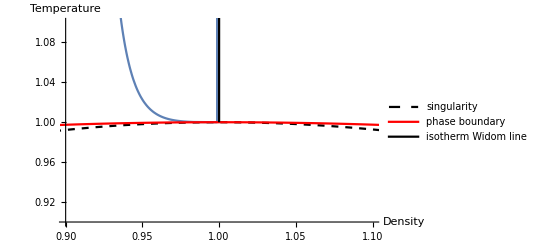

Initial point: (X_0,T_0)=(0.999,0.999999)

Angle range: (Start angle, End angle)=(0.00150075,3.14309)

Max rays: 50

```mathematica
Clear[solset]
(*Loading package for extracting domain of DE solutions*)
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"]

(*Defining the temperature T*)
T[t_]:=E^(-Z[t]);

(*Setting initial values*)
X0=0.999; (*Initial point of geodesics*)
T0=singularitysmooth[X0]+0.0000001; (*Initial point of geodesics*) (*0.297*)
StartAngle=StartSing[X0];
EndAngle=StartAngle+π;
Rays=50; (*Number of geodesics from StartAngle to EndAngle*)
tSpan=10000;

(*Solving the geodesic equations*)
solset=
Replace[
Reap[
Do[
Sow[
NDSolve[{geod1,geod2,X[0]==X0,Z[0]==-Log[T0],X'[0]==Cos[θ],T'[0]==Sin[θ]},{X,Z},{t,0,tSpan}]
],
{θ,StartAngle,EndAngle,Abs[EndAngle-StartAngle]/(Rays-1)}]][[2,1]],{{x_,y_}}->{x,y},1];

(*Plotting solutions*)
Print["T vs. x"]
Table[ParametricPlot[{X[t]/.solset[[i,1]],E^(-Z[t])/.solset[[i,2]]},{t,0.0001,InterpolatingFunctionDomain[solset[[i,1,2]]][[1,2]]},PlotRange->{{0,3},{0,2}}],{i,Length[solset]}];
Prepend[%,Plot[0.25 (-3.+t)^2 t,{t,0,3},PlotRange->{{0.9,1.1},{0.9,1.1}},PlotStyle->{Black,Dashed},PlotLegends->{"singularity"},AxesLabel->{"Density","Temperature"}]];
Append[%,Plot[pdTxsmooth[t],{t,0,3},PlotStyle->{Red},PlotLegends->{"phase boundary"}]];
Append[%,ParametricPlot[{1,t},{t,1,50},PlotStyle->{Black},PlotLegends->{"isotherm Widom line"}]];
%//Show
Print["Initial point: (X_0,T_0)=","(",X0,",",T0,")" ]
Print["Angle range: (Start angle, End angle)=","(",StartAngle,",",EndAngle,")" ]
Print["Max rays: ", Rays]
```

All trajectories 2 (single source point)*

```mathematica
Clear[solset1]
(*Loading package for extracting domain of DE solutions*)
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"]

(*Defining the temperature T*)
T[t_]:=E^(-Z[t]);

(*Setting initial values*)
Subscript[X, 0]=0.3333; (*Initial point of geodesics*)
Subscript[T, 0]=0.297; (*Initial point of geodesics*) (*0.297*)
StartAngle=0;
EndAngle=π;
Rays=20; (*Number of geodesics from StartAngle to EndAngle*)
tSpan=7;

(*Solving the geodesic equations*)
solset1=
Replace[
Reap[
Do[
Sow[
NDSolve[{geod1,geod2,X[0]==Subscript[X, 0],Z[0]==-Log[Subscript[T, 0]],X'[0]==Cos[θ],T'[0]==Sin[θ]},{X,Z},{t,0,tSpan}]
],
{θ,StartAngle,EndAngle,Abs[EndAngle-StartAngle]/(Rays-1)}]][[2,1]],{{x_,y_}}->{x,y},1];

(*Plotting solutions*)
Print["T vs. x"]
Table[ParametricPlot[{X[t]/.solset1[[i,1]],E^(-Z[t])/.solset1[[i,2]]},{t,0.0001,InterpolatingFunctionDomain[solset1[[i,1,2]]][[1,2]]},PlotRange->{{0.325,0.335},{0.295,0.3}}],{i,Length[solset1]}];
Prepend[%,Plot[{pdTxsmooth[t],2 (-1+t)^2 t},{t,0.001,1},PlotRange->{{0,1},{0,1}},PlotStyle->{Red,{Black,Dashed}},PlotLegends->{"Phase boundary","Singularity"},AxesLabel->{"Density","Temperature"}]];
%//Show
Print["Initial point: (X_0,T_0)=","(",Subscript[X, 0],",",Subscript[T, 0],")" ]
Print["Angle range: (Start angle, End angle)=","(",StartAngle,",",EndAngle,")" ]
Print["Max rays: ", Rays]
```

```mathematica
pdTxsmooth[X0]
```

0.9999